```mathematica
(* User input *)

SeqFile="Unique species CTDs.fasta";

seq=Import[SeqFile,"Sequence"];
header=Import[SeqFile,"Header"];

FensterSize=5(*Define the window size for analysis!*);

Print[StringJoin[ToString[Length[seq]]," sequences loaded!"]]
Print[Style["Program initiated!",Bold,Blue]]
```

61 sequences loaded!

Program initiated!

61 sequences and 61 header imported!

Homo sapiens CTD

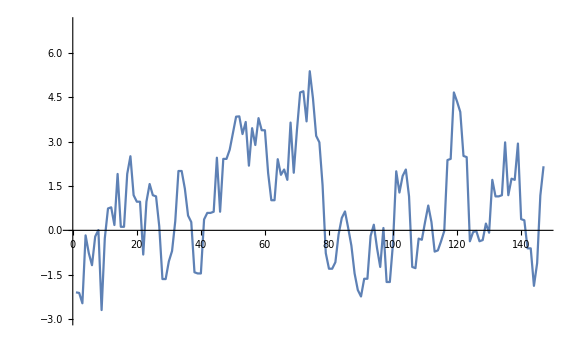

Sus scrofa CTD

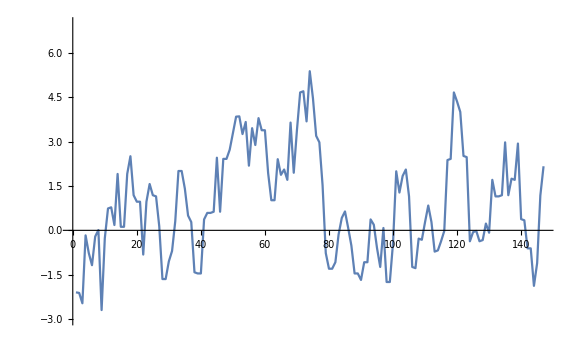

Heterocephalus glaber CTD

-Graphics-

Pantholops hodgsonii CTD

-Graphics-

Pteropus alecto CTD

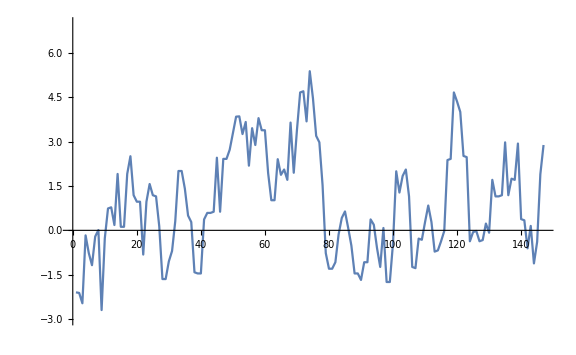

Ovis aries musimon CTD

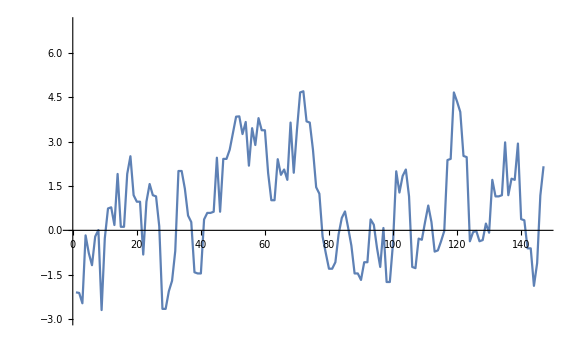

Ovis aries CTD

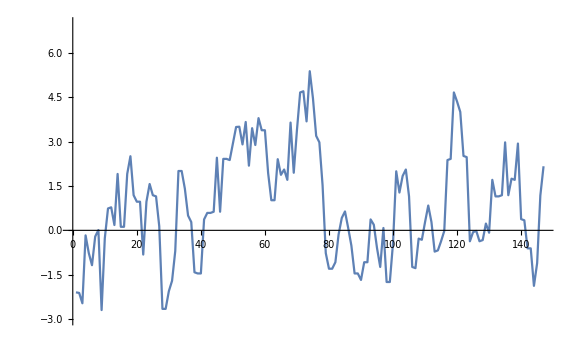

Eurypyga helias CTD

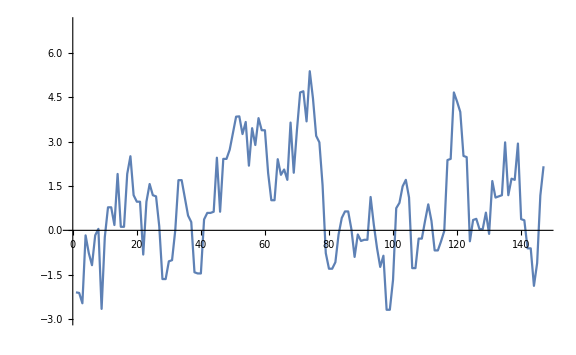

Chlamydotis macqueenii CTD

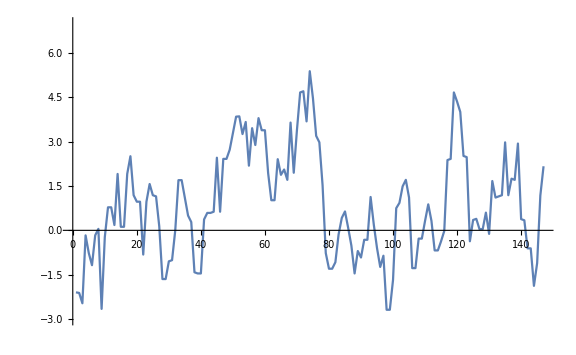

Mus musculus CTD

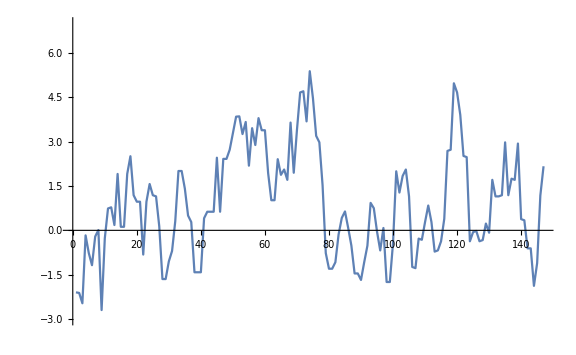

Ficedula albicollis CTD

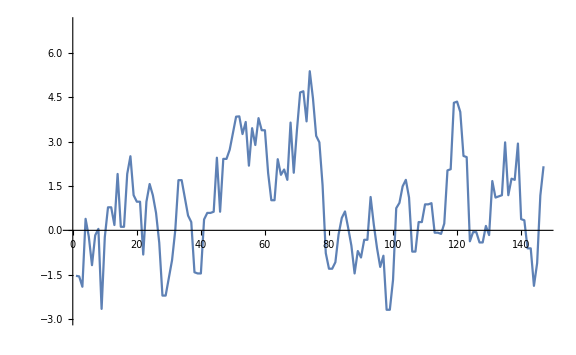

Pongo abelii CTD

-Graphics-

Callithrix jacchus CTD

-Graphics-

Sarcophilus harrisii CTD

-Graphics-

Balaenoptera acutorostrata scammoni CTD

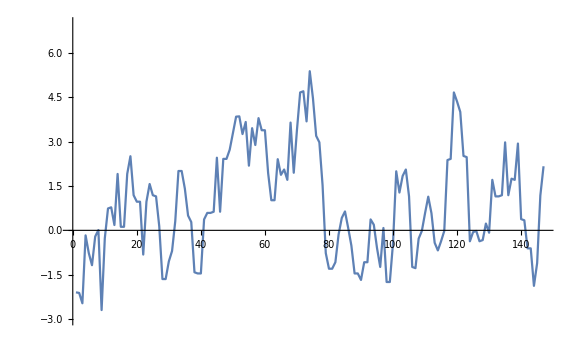

Bos taurus CTD

-Graphics-

Ursus maritimus CTD

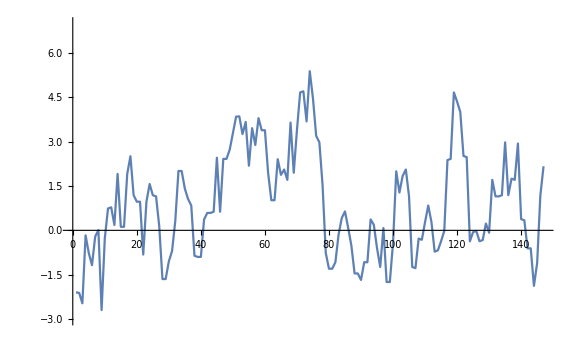

Ailuropoda melanoleuca CTD

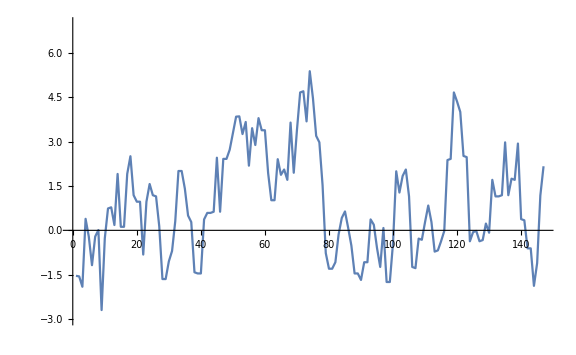

Ornithorhynchus anatinus CTD

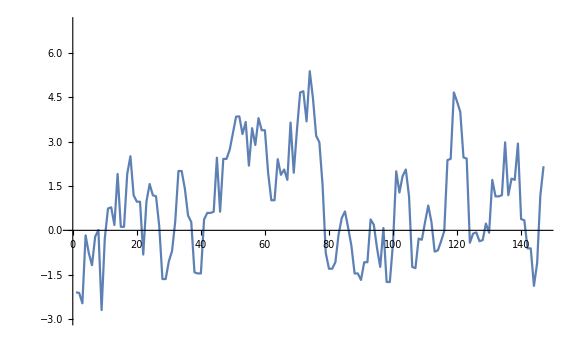

Equus caballus CTD

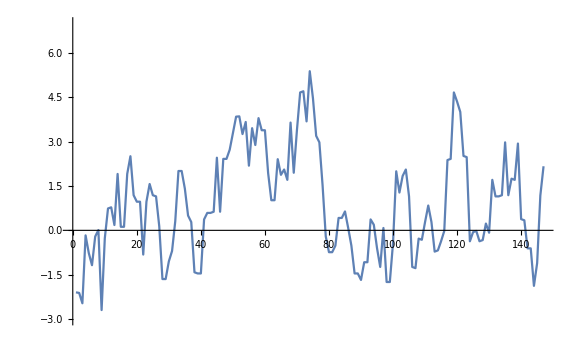

Orycteropus afer afer CTD

-Graphics-

Felis catus CTD

-Graphics-

Loxodonta africana CTD

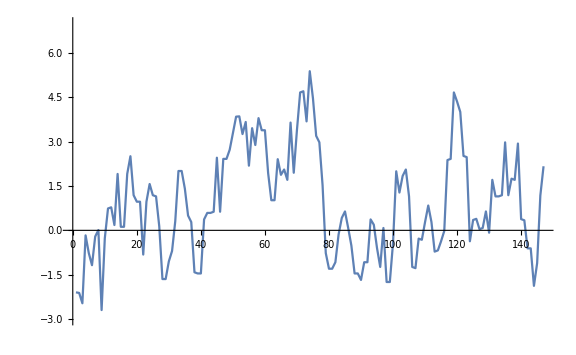

Chrysochloris asiatica CTD

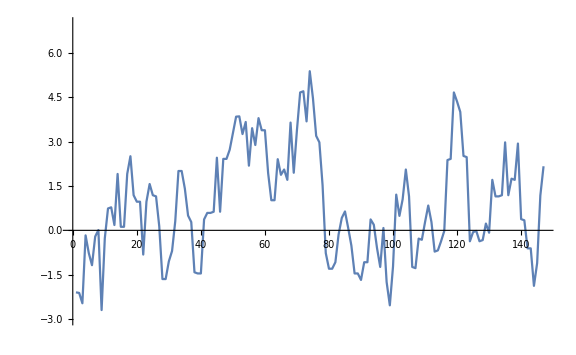

Sorex araneus CTD

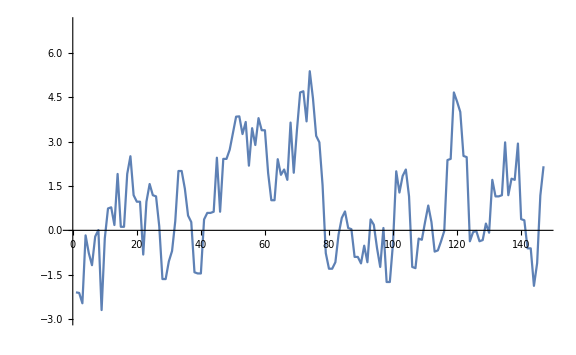

Miniopterus natalensis CTD

-Graphics-

Condylura cristata CTD

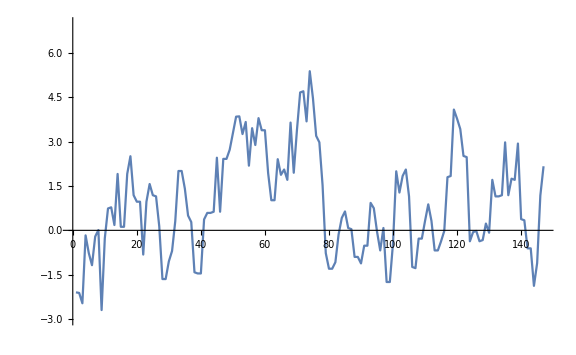

Myotis lucifugus CTD

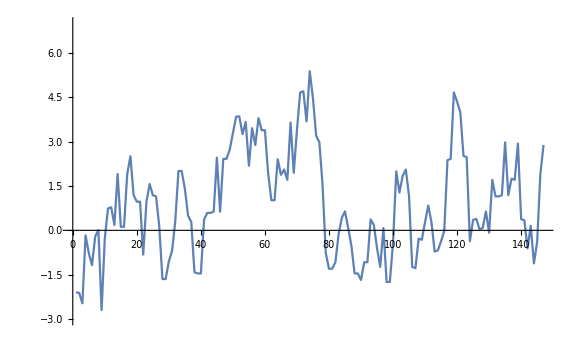

Erinaceus europaeus CTD

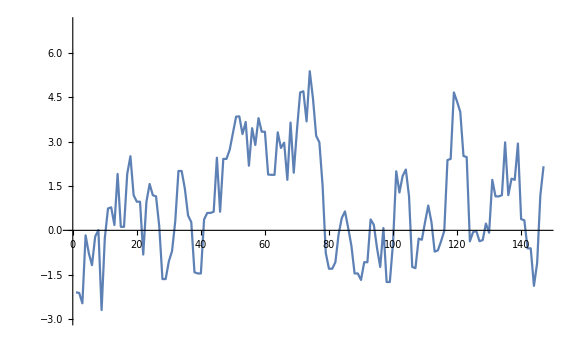

Elephantulus edwardii CTD

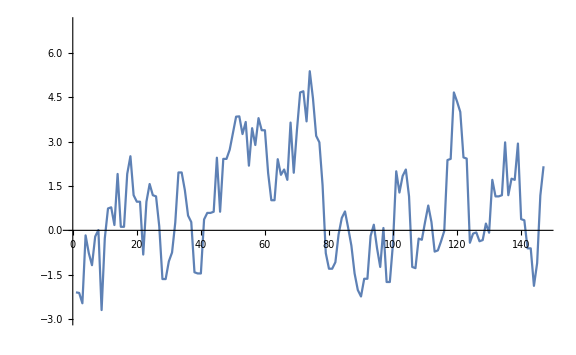

Microcebus murinus CTD

-Graphics-

Cercocebus atys CTD

-Graphics-

Octodon degus CTD

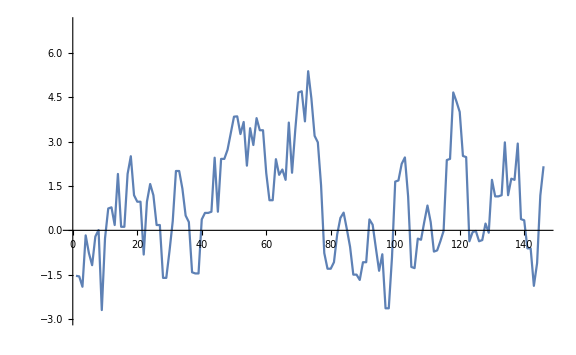

Melopsittacus undulatus CTD

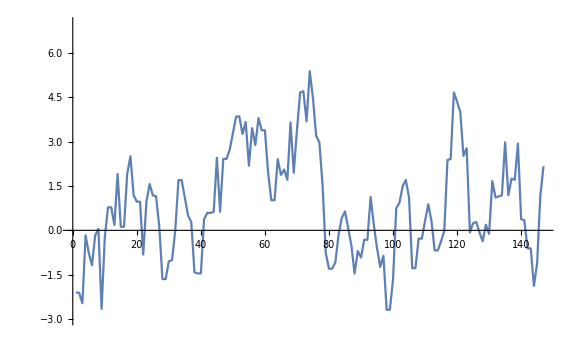

Pelecanus crispus CTD

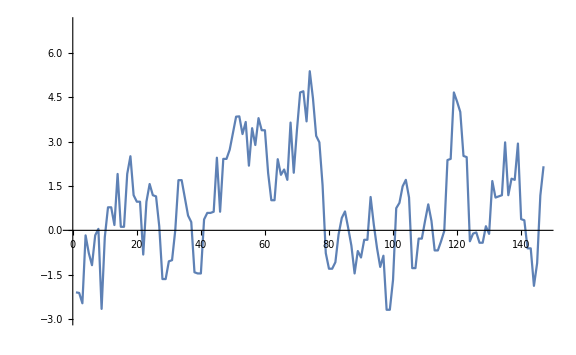

Pseudopodoces humilis CTD

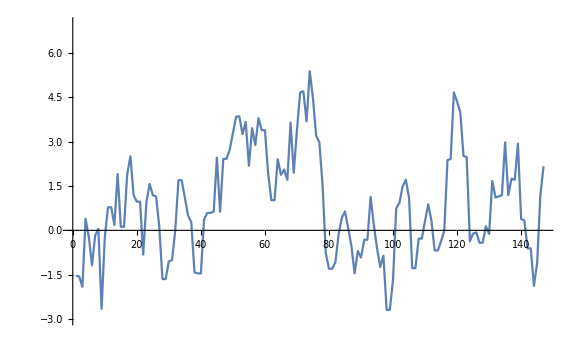

Zonotrichia albicollis CTD

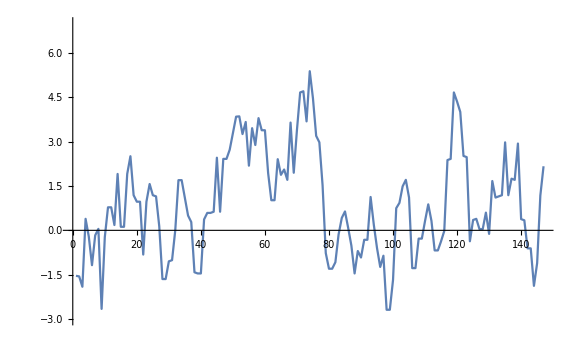

Falco peregrinus CTD

-Graphics-

Alligator sinensis CTD

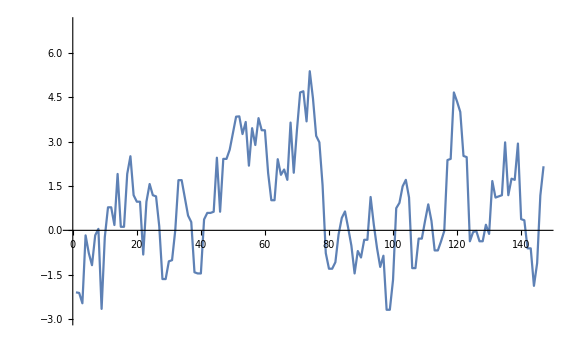

Pygoscelis adeliae CTD

-Graphics-

Cariama cristata CTD

-Graphics-

Cuculus canorus CTD

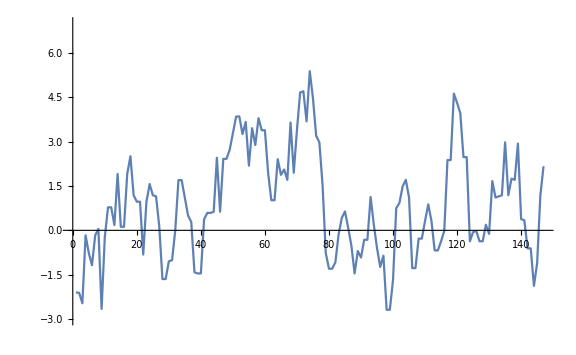

Aptenodytes forsteri CTD

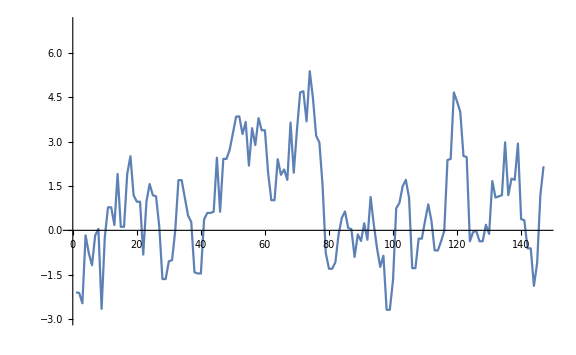

Taeniopygia guttata CTD

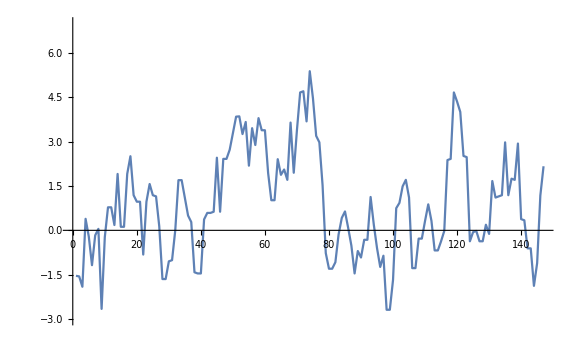

Meleagris gallopavo CTD

-Graphics-

Caprimulgus carolinensis CTD

-Graphics-

Calypte anna CTD

-Graphics-

Apteryx australis mantelli CTD

-Graphics-

Charadrius vociferus CTD

-Graphics-

Opisthocomus hoazin CTD

-Graphics-

Corvus cornix cornix CTD

-Graphics-

Tauraco erythrolophus CTD

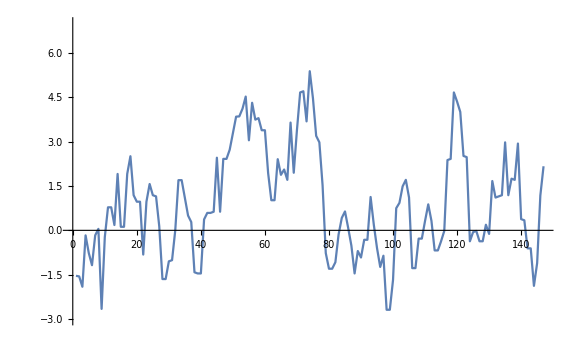

Struthio camelus australis CTD

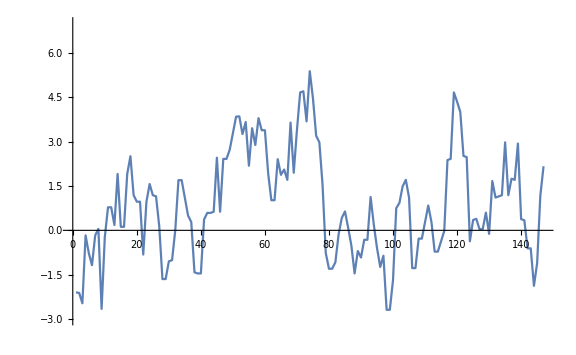

Gallus gallus CTD

-Graphics-

Phoenicopterus ruber ruber CTD

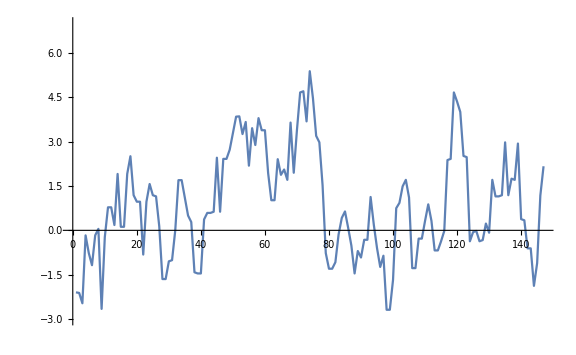

Lepidothrix coronata CTD

-Graphics-

Amazona aestiva CTD

-Graphics-

Tinamus guttatus CTD

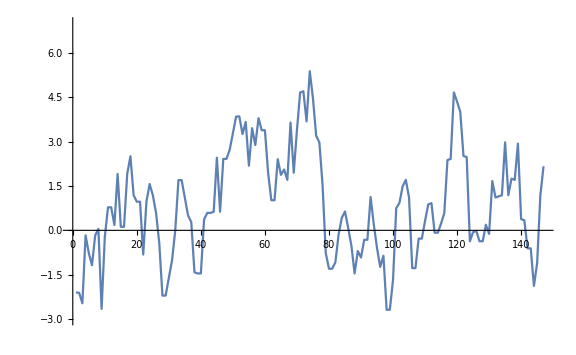

Chrysemys picta bellii CTD

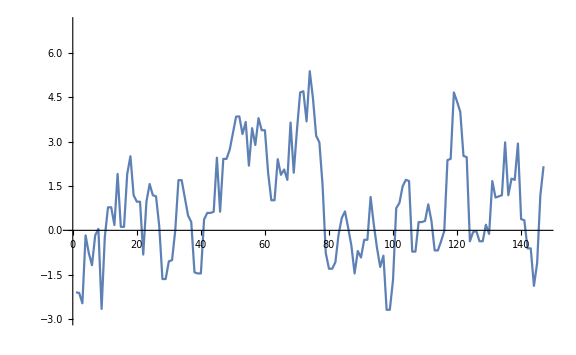

Phaethon lepturus CTD

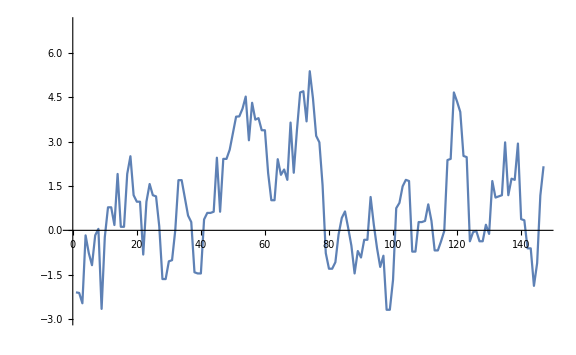

Sturnus vulgaris CTD

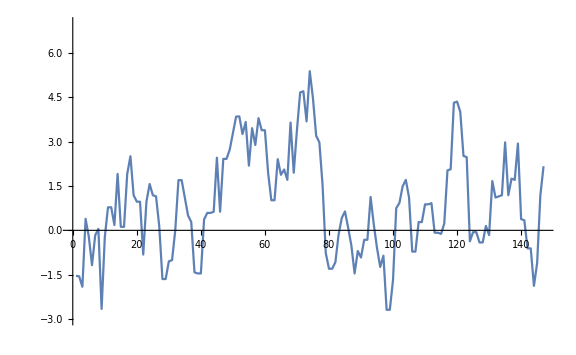

Hydrophobicity:

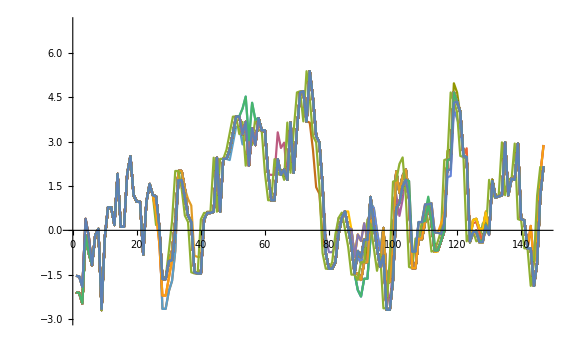

HydroWindowPlot.pdf

```mathematica
(* Go! *)

Seq=seq;
Header=header;

Print[Length[Seq]," sequences and ",Length[Header], " header imported!"]

Hydro={1.79,1.8,1.7,1.23,1.22,2.25,0.96,0.31,0.72,-0.6,-0.22,0.26,1.54,0.00,-0.04,-0.77,-0.64,0.13,-0.99,-1.01};
(* Values obtained from original publication Fauchere and Pliska, 1983 *)


raus={};
AllWindowHydro={};
Do[{holen=Seq[[a]],
Ntotal=StringLength[holen];
Hydrophobicity=(Hydro[[1]]*StringCount[holen, "F"]+
Hydro[[2]]*StringCount[holen, "I"]+
Hydro[[3]]*StringCount[holen, "L"]+
Hydro[[4]]*StringCount[holen, "M"]+
Hydro[[5]]*StringCount[holen, "V"]+
Hydro[[6]]*StringCount[holen, "W"]+
Hydro[[7]]*StringCount[holen, "Y"]+
Hydro[[8]]*StringCount[holen, "A"]+
Hydro[[9]]*StringCount[holen, "P"]+
Hydro[[10]]*StringCount[holen, "N"]+
Hydro[[11]]*StringCount[holen, "Q"]+
Hydro[[12]]*StringCount[holen, "T"]+
Hydro[[13]]*StringCount[holen, "C"]+
Hydro[[14]]*StringCount[holen, "G"]+
Hydro[[15]]*StringCount[holen, "S"]+
Hydro[[16]]*StringCount[holen, "D"]+
Hydro[[17]]*StringCount[holen, "E"]+
Hydro[[18]]*StringCount[holen, "H"]+
Hydro[[19]]*StringCount[holen, "K"]+
Hydro[[20]]*StringCount[holen, "R"]);

RelativeHydrophobicity=Hydrophobicity/Ntotal;

n1=ToLowerCase[holen];
raus=AppendTo[raus,{n1,RelativeHydrophobicity}];


(* Do a sliding window analysis *)

WindowTempHydro={};
Do[{b1=StringTake[holen,{b,b+(FensterSize-1)}],

Btotal=StringLength[b1];

bHydrophobicity=(Hydro[[1]]*StringCount[b1, "F"]+
Hydro[[2]]*StringCount[b1, "I"]+
Hydro[[3]]*StringCount[b1, "L"]+
Hydro[[4]]*StringCount[b1, "M"]+
Hydro[[5]]*StringCount[b1, "V"]+
Hydro[[6]]*StringCount[b1, "W"]+
Hydro[[7]]*StringCount[b1, "Y"]+
Hydro[[8]]*StringCount[b1, "A"]+
Hydro[[9]]*StringCount[b1, "P"]+
Hydro[[10]]*StringCount[b1, "N"]+
Hydro[[11]]*StringCount[b1, "Q"]+
Hydro[[12]]*StringCount[b1, "T"]+
Hydro[[13]]*StringCount[b1, "C"]+
Hydro[[14]]*StringCount[b1, "G"]+
Hydro[[15]]*StringCount[b1, "S"]+
Hydro[[16]]*StringCount[b1, "D"]+
Hydro[[17]]*StringCount[b1, "E"]+
Hydro[[18]]*StringCount[b1, "H"]+
Hydro[[19]]*StringCount[b1, "K"]+
Hydro[[20]]*StringCount[b1, "R"]);

bRelativeHydrophobicity=bHydrophobicity/Btotal;
WindowTempHydro=AppendTo[WindowTempHydro,bHydrophobicity];

},{b,1,StringLength[holen]-FensterSize}];

AllWindowHydro=AppendTo[AllWindowHydro,WindowTempHydro],

(* Show the hydrophobicity plot *)
Print[Header[[a]]],
Print[ListLinePlot[WindowTempHydro,ImageSize->Large,PlotRange->{Automatic,{-3,7}},Frame->False]]

},{a,1,Length[Seq]}]

Sortiert=Sort[raus,#1[[2]]<#2[[2]]&];
TableForm[Sortiert];



(* Show a summary plot of all analyzed sequences *)

Print["Hydrophobicity:"]
HydroWindowPlot=ListLinePlot[AllWindowHydro,ImageSize->Large,PlotRange->{Automatic,{-3,7}},Frame->False]

(* Export the data! *)

SetDirectory[DirectoryName[SeqFile]];
Export["HydroWindowPlot.pdf",HydroWindowPlot]
```